Because I took a Differential Equations class as a High School senior, I didn’t need to do much work on this Bset other than figuring out Mathematica syntax. My work is below.

```mathematica
eqn=y'[x]+4/x y[x]==x^3 y[x]^2
sol=DSolve[eqn,y[x],x][[1]]
```

(4 y[x])/x+y'[x]==x^3 y[x]^2

{y[x]→1/(x^4 (C[1]-Log[x]))}

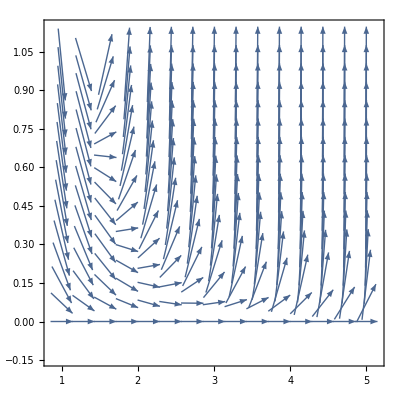

```mathematica
neweqn=Solve[eqn,y'[x]][[1,1,2]]/.y[x]->y;
VectorPlot[Normalize@{1,neweqn},{x,1,5},{y,0,1}]
```

```mathematica
Manipulate[Plot[y[x]/.sol/.{C[1]->const},{x,0,2}],{const,0,10}]
```

ReplaceAll::reps: {P/cp+ⅇ^(-(cp t)/Q) C[1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2.08 ⅇ^(-(cp t)/Q)+P/cp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2.08 2.71828^(-(1. cp t)/Q)+P/cp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

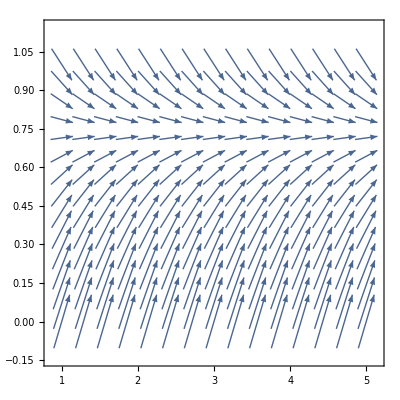

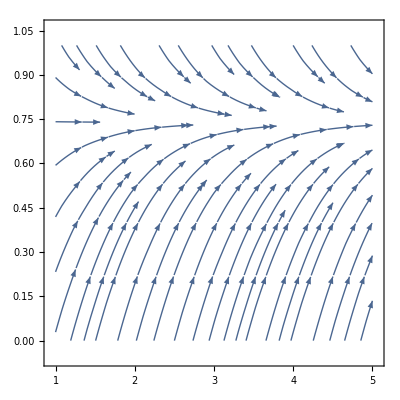

```mathematica
neweqn=-y+Cos[y];
VectorPlot[Normalize@{1,neweqn},{x,1,5},{y,0,1}]
StreamPlot[Normalize@{1,neweqn},{x,1,5},{y,0,1}]
```

```mathematica
N[Log[1/1000]]
```

-6.90776

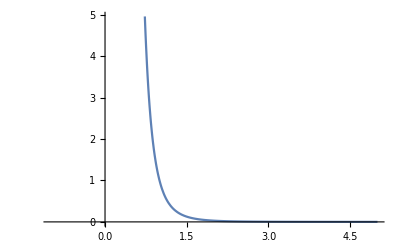

```mathematica
Manipulate[N[x Log[x]],{x,0,5}]
Plot[N[x^-5.1],{x,-1,5}]
```

```mathematica
DSolve[y'[x]==y[x]+Cos[y[x]],y[x],x]
```

{{y[x]→InverseFunction[∫_1^#1 1/(Cos[K[1]]+K[1])ⅆK[1]&][x+C[1]]}}

```mathematica
eqn=Q T'[t]==P-cp T[t]
sol=DSolveValue[eqn,T[t],t]
```

Q T'[t]==P-cp T[t]

P/cp+ⅇ^(-(cp t)/Q) C[1]

```mathematica
Manipulate[Plot[sol/.{P->2,cp->3,Q->1}/.{C[1]->const},{t,0,2},PlotRange->{-5,5}],{const,-10,10}]
```